# read mesh and make Graphics primitives

```mathematica
fn="~/yunomi/yunomi1.msh";
```

```mathematica
stream1=OpenRead[fn];
{n1,n2,n3}=Read[stream1,{Number,Number,Number}]
```

{1538,2776,300}

```mathematica
n1+n2+n3
```

4614

```mathematica
frm=Table[{Real,Real,Number},{n1}];
```

```mathematica
p=Read[stream1,frm];
```

```mathematica
Dimensions[p]
```

{1538,3}

```mathematica
p1=Table[{p[[i,1]],p[[i,2]]},{i,Length[p]}];
```

```mathematica
Dimensions[p1]
```

{1538,2}

```mathematica
frm=Table[{Number,Number,Number,Number},{n2}];
```

```mathematica
tr=Read[stream1,frm];
```

```mathematica
Dimensions[tr]
```

{2776,4}

```mathematica
tr1=Table[{tr[[i,1]],tr[[i,2]],tr[[i,3]],tr[[i,1]]},{i,Length[tr]}];
```

```mathematica
Dimensions[tr1]
```

{2776,4}

```mathematica
frm=Table[{Number,Number,Number},{n3}];
```

```mathematica
vt=Read[stream1,frm];
```

```mathematica
Dimensions[vt]
```

{300,3}

```mathematica
Close[stream1];
```

```mathematica
p2=Map[p1[[#]]&,tr1];
```

```mathematica
p2[[1]]
```

{{0.115243,0.695377},{0.122814,0.687289},{0.13,0.698975},{0.115243,0.695377}}

```mathematica
Length[tr1]
```

2776

```mathematica
lp1=Map[Line,p2];
```

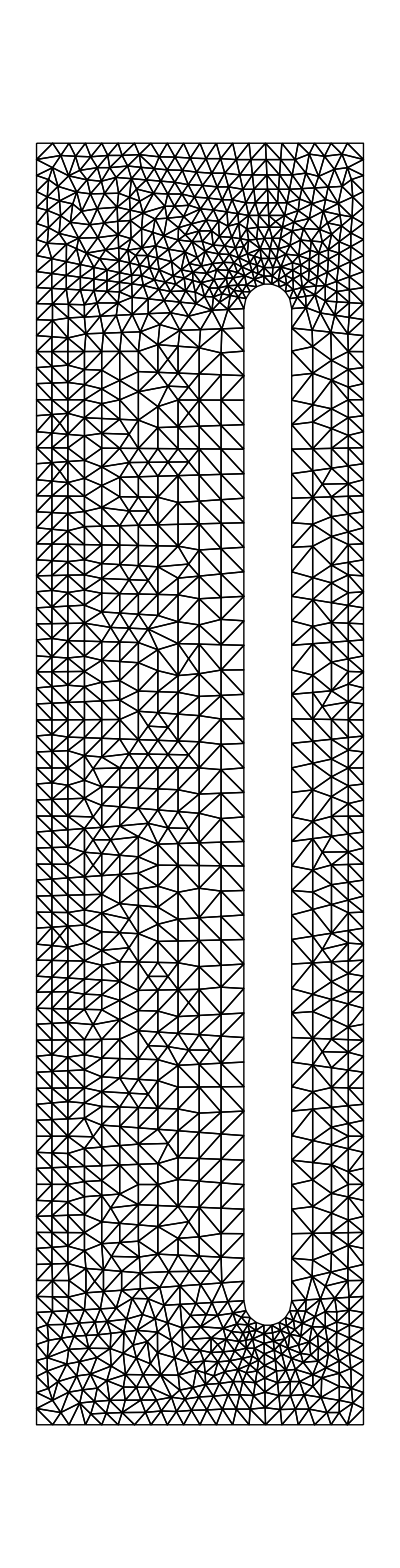

```mathematica
Show[Graphics[lp1],AspectRatio->4,PlotRange->All]
```

# Read values of the solution

```mathematica
fn="~/Documents/NACA0012/NACA0012.out";
```

```mathematica
stream1=OpenRead[fn];
```

```mathematica
n4=Read[stream1,Number]
```

3034

```mathematica
frm=Table[Real,{n4}];
```

```mathematica
r=Read[stream1,frm];
```

```mathematica
Close[stream1];
```

```mathematica
Dimensions[r]
```

{3034}

## Normalization of values of solution

```mathematica
m1=Min[r];
```

```mathematica
r=r-m1;
```

```mathematica
m1=Max[r];
```

```mathematica
r=r/m1;
```

```mathematica
r2=Table[(r[[tr[[i,1]]]]+r[[tr[[i,2]]]]+r[[tr[[i,3]]]])/3.0,{i,Length[tr]}];
```

## Make Colored polygon

```mathematica
p3=Table[{(p1[[tr[[i,1]]]]+p1[[tr[[i,2]]]])*0.5,(p1[[tr[[i,2]]]]+p1[[tr[[i,3]]]])*0.5,(p1[[tr[[i,3]]]]+p1[[tr[[i,1]]]])*0.5},{i,Length[tr]}];
```

```mathematica
plg=Table[{{Hue[r[[tr[[i,1]]]]],Polygon[{p2[[i,1]],p3[[i,1]],p3[[i,3]]}]},{Hue[r2[[i]]],Polygon[{p3[[i,1]],p3[[i,2]],p3[[i,3]]}]},{Hue[r[[tr[[i,2]]]]],Polygon[{p2[[i,2]],p3[[i,2]],p3[[i,1]]}]},{Hue[r[[tr[[i,3]]]]],Polygon[{p2[[i,3]],p3[[i,3]],p3[[i,2]]}]}},{i,Length[tr]}];
```

## Draw the result

```mathematica
Show[Graphics[plg],PlotRange->{{-.25,1.25},{-1,1}},AspectRatio->2/1.5];
```

```mathematica
Show[Graphics[plg],PlotRange->All,AspectRatio->1];
```